Jak vypadají ostrovy našich obyvatel? (Překvapení!!! Jako jejich obyvatelé.)

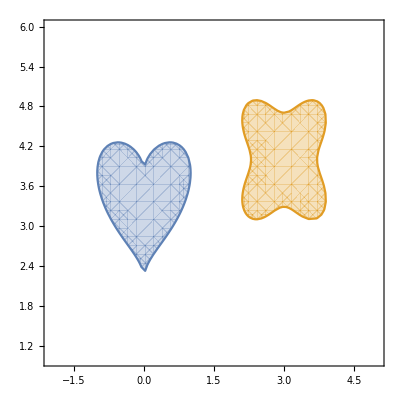

```mathematica
mapa =RegionPlot[{x^2+(5(y-3)/4-Sqrt[Abs[x]])^2 ≤ 1,(2(x-3)^2+2(y-4)^2)^3-40(x-3)^2 *(y-4)^2 ≤ 1},{x,-2,5},{y,1,6}]
```

Výpočet - Jak postavit most mezi národy?

```mathematica
g1=x1^2+(5(x2-3)/4-(x1^2+0.001^2)^(1/4))^2;
g2=(2(y1-3)^2+2(y2-4)^2)^3-40(y1-3)^2 *(y2-4)^2;
f = (x1-y1)^2 + (x2-y2)^2;
smallLagrangian= Piecewise[{{-λ^2 /(2ρ),λ+ρ*g ≤ ρ},{λ(g-1)+ρ/2 (g-1)^2,λ+ρ*g > ρ}}];
```

```mathematica
Lagrangian = f + ReplaceAll[ReplaceAll[smallLagrangian,g->g1],λ->λ1]+ReplaceAll[ReplaceAll[smallLagrangian,g->g2],λ->λ2];
```

```mathematica
DfDx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2}} ];
D2fDxx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2},2} ];
ρ=0.001;
```

```mathematica
{x1,x2,y1,y2,λ1,λ2}={1.,4.,2.,3.,0.,0.};
i=0;
history1={{x1,x2}};
history2={{y1,y2}};
While[ Sqrt[DfDx.DfDx]>10^-12&&i≤15,
dx=-Inverse[D2fDxx].DfDx;
{x1,x2,y1,y2,λ1,λ2}={x1,x2,y1,y2,λ1,λ2}+dx;
AppendTo[ history1,{x1,x2} ];
AppendTo[ history2,{y1,y2} ];
i=i+1;
Print[ "i=",i," xy=",{x1,x2,y1,y2,λ1,λ2}," |Δxy|=",Sqrt[dx.dx]," |DfDxy|=",Sqrt[DfDx.DfDx] ]
]
```

i=1 xy={1.34696,2.92852,2.03224,3.17312,0.783097,0.0234843} |Δxy|=1.3832 |DfDxy|=8.54974

i=2 xy={1.21908,3.53476,2.01258,3.38079,0.609376,0.0310429} |Δxy|=0.676485 |DfDxy|=4.22907

i=3 xy={1.06083,3.7438,2.06585,3.5418,0.837168,0.0514818} |Δxy|=0.387052 |DfDxy|=1.84534

i=4 xy={0.991453,3.66979,2.10466,3.47882,1.03297,0.0709303} |Δxy|=0.233408 |DfDxy|=0.210951

i=5 xy={0.989227,3.67819,2.11147,3.48409,1.0555,0.0781683} |Δxy|=0.0266384 |DfDxy|=0.0101657

i=6 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.078469} |Δxy|=0.000975099 |DfDxy|=0.0000212378

i=7 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δxy|=3.50802×10^-6 |DfDxy|=3.08322×10^-10

i=8 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δxy|=1.86466×10^-11 |DfDxy|=1.33787×10^-14

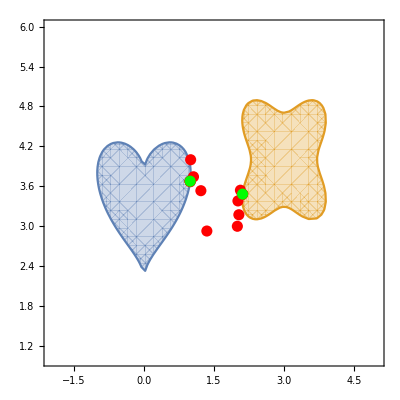

```mathematica
Show[mapa,
Graphics[{Red,PointSize[0.02],Point[#]}]&/@history1⟦;;-2⟧,
Graphics[{Green,PointSize[0.02],Point[#]}]&/@history1⟦{-1}⟧,Graphics[{Red,PointSize[0.02],Point[#]}]&/@history2⟦;;-2⟧,
Graphics[{Green,PointSize[0.02],Point[#]}]&/@history2⟦{-1}⟧
]
```

Velké sjednocení

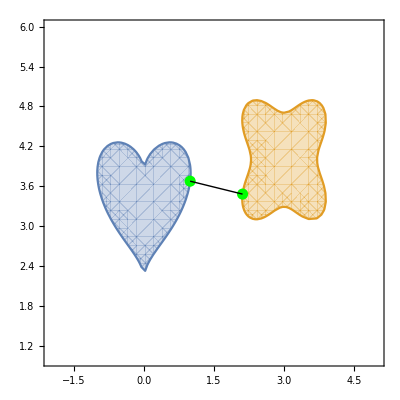

```mathematica
Show[mapa,Graphics[{Green,PointSize[0.02],Point[#]}]&/@history1⟦{-1}⟧,Graphics[{Green,PointSize[0.02],Point[#]}]&/@history2⟦{-1}⟧,Graphics[Line[{{x1,x2},{y1,y2}}]]]
```